# ODE

## Initial Value Problem

## Case 1 : One first - order ODE

Solve an IVP of the type :

dy/dx=f(x,y(x))
y(x_0)=y_0

As an example consider :

dy/dx=-y(y-2)
y(0)=1

### Symbolic Solution

```mathematica
DSolve[{y'[t]==-y[t]*(y[t]-2)},y,t]
```

{{y→Function[{t},(2 ⅇ^(2 t))/(ⅇ^(2 t)+ⅇ^(2 C[1]))]}}

```mathematica
dsSol=DSolve[{y'[t]==-y[t](y[t]-2),y[0]==1},y,t][[1]]
```

{y→Function[{t},(2 ⅇ^(2 t))/(1+ⅇ^(2 t))]}

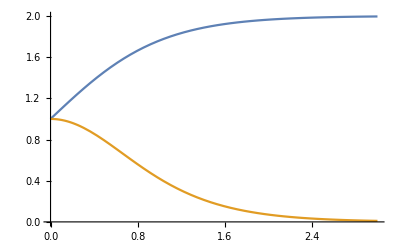
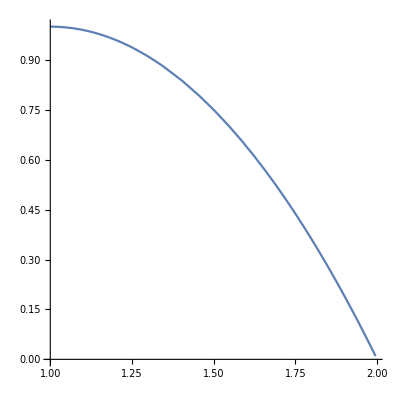

```mathematica
{Plot[Evaluate[{y[t],y'[t]}/.dsSol],{t,0,3}],ParametricPlot[Evaluate[{y[t],y'[t]}/.dsSol],{t,0,3}]}
```

### Euler Method

```mathematica
f[x_,y_]:=-y(y-2);
```

```mathematica
{eSolx,eSoly}=eulerNDSolve[f,1,{0,3,100}];
```

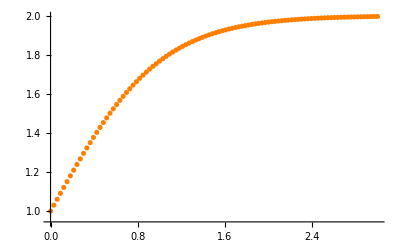

```mathematica
ListPlot[eSoly,PlotStyle->Orange,DataRange->{0,3}]
```

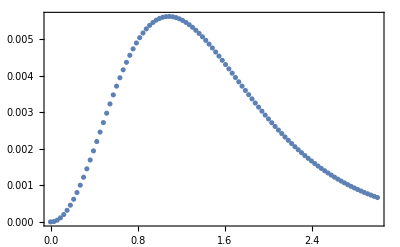

```mathematica
ListPlot[Abs[(y[eSolx]/.dsSol)-eSoly],DataRange->{0,3},Frame->True]
```

### Runge - Kutta order 4

```mathematica
{eSolx2,eSoly2}=RK4NDSolve[f,1,{0,3,100}];
```

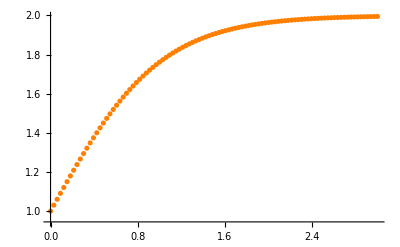

```mathematica
ListPlot[eSoly2,PlotStyle->Orange,DataRange->{0,3}]
```

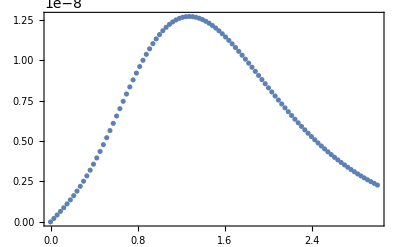

```mathematica
ListPlot[Abs[(y[eSolx2]/.dsSol)-eSoly2],DataRange->{0,3},Frame->True]
```

### Mathematica NDSolve

```mathematica
ndsSol=NDSolve[{y'[t]==-y[t](y[t]-2),y[0]==1},y,{t,0,3}][[1]]
```

{y→InterpolatingFunction[…]}

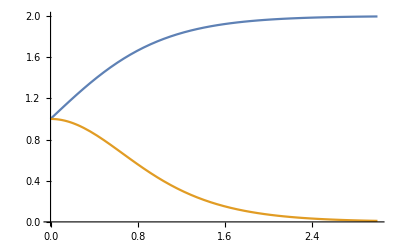
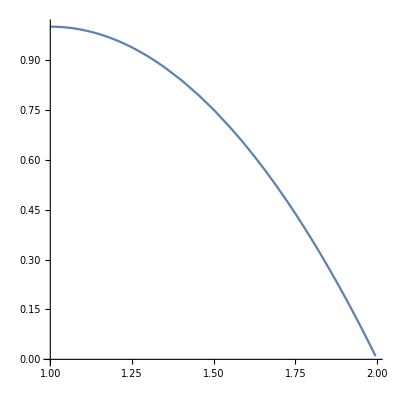

```mathematica
{Plot[Evaluate[{y[t],y'[t]}/.ndsSol],{t,0,3}],ParametricPlot[Evaluate[{y[t],y'[t]}/.ndsSol],{t,0,3}]}
```

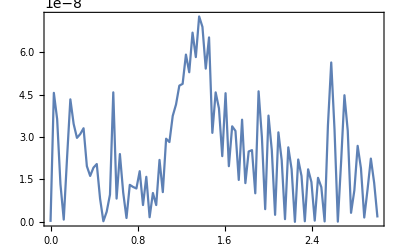

```mathematica
With[{sym=y[eSolx]/.dsSol,num=y[eSolx]/.ndsSol},
ListLinePlot[Abs[sym-num]/sym,Frame->True,DataRange->{0,3}]]
```

### Family of solutions

```mathematica
familyOfSolutions[a_,b_,step_]:=Table[NDSolve[{y'[t]==-y[t](y[t]-2),y[0]==s},y,{t,0,3}][[1]],{s,a,b,step}]
```

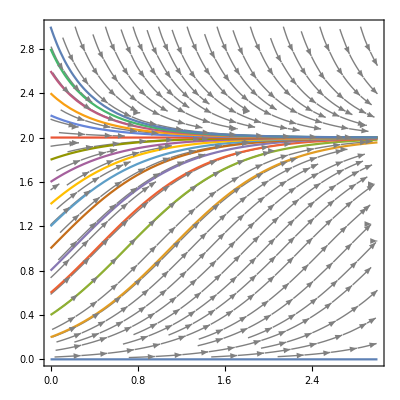

```mathematica
Show[StreamPlot[{1,-y(y-2)},{t,0,3},{y,0,3},StreamStyle->{Gray,Gray},StreamColorFunction->None],
Plot[Evaluate[y[t]/.familyOfSolutions[0,3,0.2]],{t,0,3},PlotRange->All]]
```

## Case 2 : Several 1 - order ODEs

### Euler Nd

Solve an IVP of the type:

(d y^(->))/dx=f(x,y^(->)(x))
y^(->)(x_0)=(y^(->))_0

As an example consider:

(d^2 x)/dx^2+ω^2 dx/dt=0

That can be transformed into a couple of first order ODE:

y_1=x->dy_1/dt=dx/dt=y_2
y_2=dx/dt->dy_2/dt=(d^2 x)/(d^2 t)=-ω^2 dx/dt=-ω^2 y_1

### Symbolic Solution

```mathematica
DSolve[{x''[t]+ω^2 x[t]==0},x,t]
```

{{x→Function[{t},C[1] Cos[t ω]+C[2] Sin[t ω]]}}

```mathematica
dsSol=DSolve[{x''[t]+x[t]==0,x[0]==1,x'[0]==0},x,t][[1]]
```

{x→Function[{t},Cos[t]]}

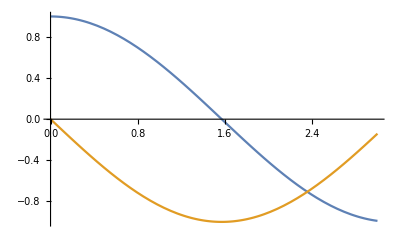
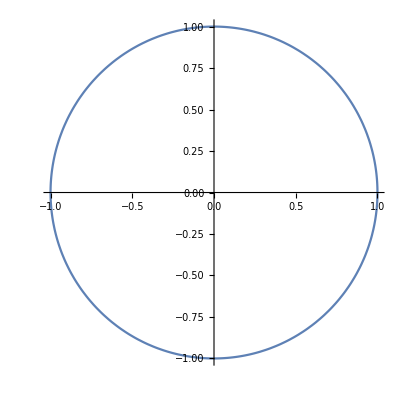

```mathematica
{Plot[Evaluate[{x[t],x'[t]}/.dsSol],{t,0,3}],ParametricPlot[Evaluate[{x[t],x'[t]}/.dsSol],{t,0,2π}]}
```

```mathematica
1/2 x[t]^2+1/2(x'[t])^2/.dsSol//Simplify
```

1/2

### Euler Method

```mathematica
f[x_,{y1_,y2_}]:={y2,-y1}
```

```mathematica
eSol=eulerNDSolve[f,{1,0},{0,2π,1000}];
```

```mathematica
eSolx=eSol[[1]];
eSoly=eSol[[2]];
```

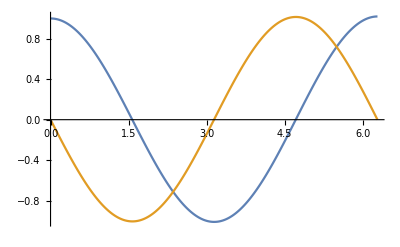
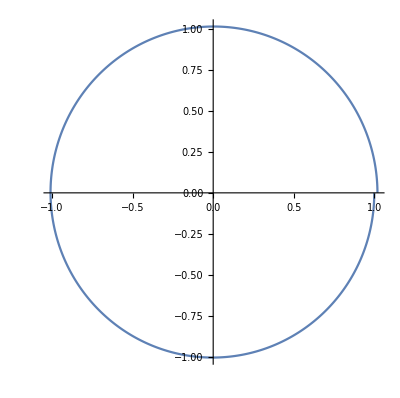

```mathematica
{ListLinePlot[eSoly,DataRange->{0,2π}],
ListLinePlot[Transpose[eSoly],AspectRatio->Automatic]}
```

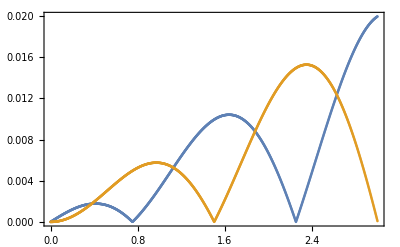
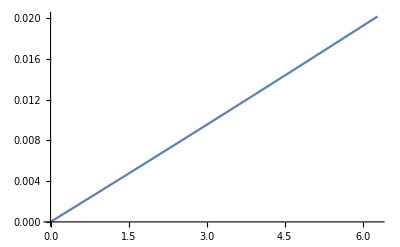

```mathematica
{ListPlot[
{Abs[(x[eSolx]/.dsSol)-eSoly[[1]]],Abs[(x'[eSolx]/.dsSol)-eSoly[[2]]]},DataRange->{0,3},Frame->True],ListLinePlot[1/2 eSoly[[1]]^2+1/2 eSoly[[2]]^2-0.5,DataRange->{0,2π}]}
```

### Runge kutta Method

```mathematica
eSol2=RK4NDSolve[f,{1,0},{0,2π,1000}];
```

```mathematica
eSolx2=eSol2[[1]];
eSoly2=eSol2[[2]];
```

```mathematica
eSoly2//Dimensions
```

{2,1000}

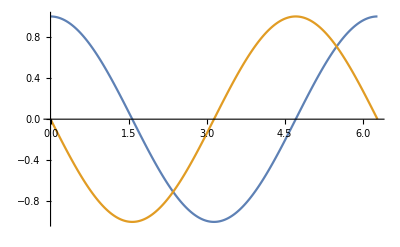
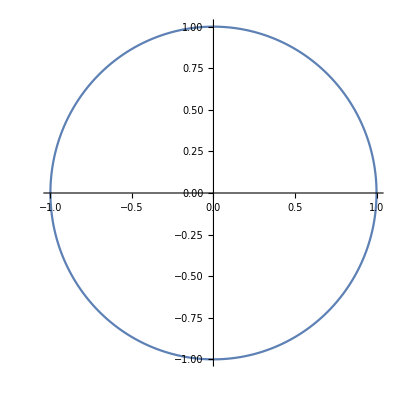

```mathematica
{ListLinePlot[eSoly2,DataRange->{0,2π}],
ListLinePlot[Transpose[eSoly2],AspectRatio->Automatic]}
```

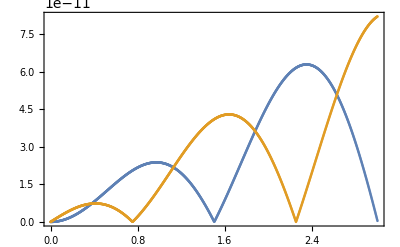
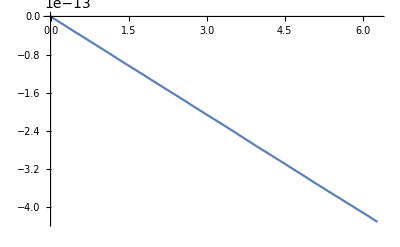

```mathematica
{ListPlot[
{Abs[(x[eSolx2]/.dsSol)-eSoly2[[1]]],Abs[(x'[eSolx2]/.dsSol)-eSoly2[[2]]]},DataRange->{0,3},Frame->True],ListLinePlot[1/2 eSoly2[[1]]^2+1/2 eSoly2[[2]]^2-0.5,DataRange->{0,2π}]}
```

### Mathematica NDSolve

```mathematica
ndsSol=NDSolve[{x''[t]+x[t]==0,x[0]==1,x'[0]==0},x,{t,0,2π}][[1]]
```

{x→InterpolatingFunction[…]}

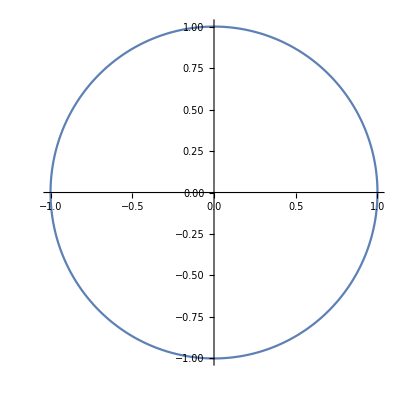
{-Graphics-,-Graphics-}

```mathematica
{Plot[Evaluate[{x[t],x'[t]}/.ndsSol],{t,0,2π}],ParametricPlot[Evaluate[{x[t],x'[t]}/.ndsSol],{t,0,2π}]}
```

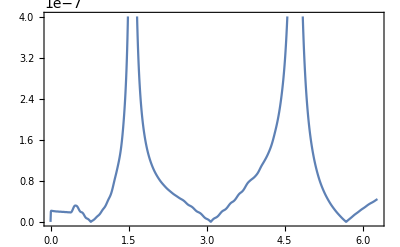

```mathematica
With[{sym=x[eSolx]/.dsSol,num=x[eSolx]/.ndsSol},
ListLinePlot[Abs[sym-num]/Abs[sym],DataRange->{0,2π},Frame->True]]
```